ConditionalExpression[1/(4 π sigma^2), Re[sigma^2]>0]

1/(4 π)

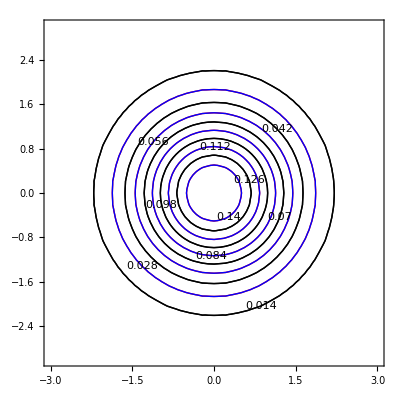

```mathematica
(*Define the 2D Gaussian function*)gaussian2D[x_,y_,sigma_]:=(1/(2*Pi*sigma^2))*Exp[-((x^2+y^2)/(2*sigma^2))]

(*Define the integral of the square of the Gaussian*)
integral=Integrate[gaussian2D[x,y,sigma]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]

(*Evaluate the integral for a particular value of sigma,e.g.,sigma=1*)
integralValue=integral/. sigma->1

(*Plot the overlapping Gaussians*)
Show[ContourPlot[gaussian2D[x,y,1],{x,-3,3},{y,-3,3},Contours->10,ContourShading->None,ContourStyle->{Thick,Red}],ContourPlot[gaussian2D[x,y,1],{x,-3,3},{y,-3,3},Contours->10,ContourShading->None,ContourStyle->{Thick,Blue},ContourLabels->True]]
```

```mathematica
(*Define the 2D Gaussian function*)gaussian2D[x_,y_,sigma_]:=(1/(2*Pi*sigma^2))*Exp[-((x^2+y^2)/(2*sigma^2))]

(*Define the product of two identical Gaussian distributions*)
productGaussian[x_,y_,sigma_]:=gaussian2D[x,y,sigma]*gaussian2D[x,y,sigma]

(*Generate the 3D plot*)
Plot3D[productGaussian[x,y,1],{x,-3,3},{y,-3,3},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"Overlapping of Two Identical Gaussian Distributions"]
```

-Graphics3D-

```mathematica
(*Define the 2D Gaussian functions with different centers*)gaussian2D1[x_,y_,sigma_,x0_,y0_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)]
gaussian2D2[x_,y_,sigma_,x1_,y1_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)]

(*Define the integral of the product of the two Gaussians*)
integralProduct[x0_,y0_,x1_,y1_,sigma_]:=NIntegrate[gaussian2D1[x,y,sigma,x0,y0]*gaussian2D2[x,y,sigma,x1,y1],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]

(*Define the distance between the centers of the Gaussians*)
distance[x0_,y0_,x1_,y1_]:=Sqrt[(x1-x0)^2+(y1-y0)^2]

(*Generate a list of distances and corresponding integral values*)
data=Table[{distance[x0,y0,x1,y1],integralProduct[x0,y0,x1,y1,1]},{x0,-5,5,5},{y0,-5,5,5},{x1,-5,5,5},{y1,-5,5,0.5}]//Flatten[#,3]&;

(*Plot the integral as a function of the distance between the centers*)
ListPlot[data,PlotRange->All,AxesLabel->{"Distance","Integral"},PlotLabel->"Overlapping Integral as a Function of Distance"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

ListPlot::lpn: data is not a list of numbers or pairs of numbers.

ListPlot[data,PlotRange→All,AxesLabel→{Distance,Integral},PlotLabel→Overlapping Integral as a Function of Distance]

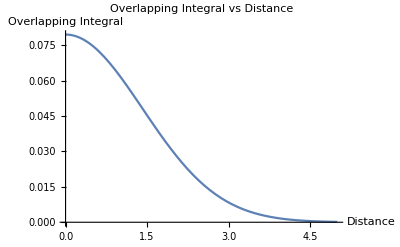

-Graphics3D-

```mathematica
(*Function to calculate the overlapping integral*)OverlappingIntegral[distance_,sigma_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Calculate and return the overlapping integral*)NIntegrate[gaussian2D1[x,y]*gaussian2D2[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]]

(*Function to generate the 2D plot of the overlapping integral vs.distance*)
PlotOverlappingIntegral[sigma_]:=Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Overlapping Integral"},PlotLabel->"Overlapping Integral vs Distance"]

(*Function to generate the 3D plot of the overlapping Gaussians*)
Plot3DOverlap[distance_,sigma_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Generate and return the 3D plot*)Plot3D[gaussian2D1[x,y]+gaussian2D2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"3D Overlap of Two Gaussian Distributions"]]

(*Call the functions to generate the plots*)
PlotOverlappingIntegral[1]
Plot3DOverlap[2,1]
```

NIntegrate::inumr: The integrand (ⅇ^(1/2 (-x^2-y^2)+1/2 (-Plus[«2»]^2-y^2)))/(4 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

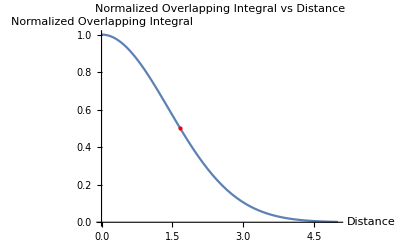

-Graphics3D-

```mathematica
(*Function to calculate and normalize the overlapping integral*)OverlappingIntegral[distance_,sigma_]:=Module[{x0,y0,x1,y1,overlappingIntegral,normalizationFactor},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Calculate the overlapping integral*)overlappingIntegral=NIntegrate[gaussian2D1[x,y]*gaussian2D2[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Calculate the normalization factor*)normalizationFactor=NIntegrate[gaussian2D1[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Normalize and return the overlapping integral*)overlappingIntegral/normalizationFactor]

(*The rest of the code remains the same as previously provided*)

(*Function to generate the 2D plot of the overlapping integral vs.distance*)
PlotOverlappingIntegral[sigma_]:=Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance"]

(*Function to generate the 3D plot of the overlapping Gaussians*)
Plot3DOverlap[distance_,sigma_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Generate and return the 3D plot*)Plot3D[gaussian2D1[x,y]+gaussian2D2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"3D Overlap of Two Gaussian Distributions"]]

(*Call the functions to generate the plots*)
(*Function to calculate and normalize the overlapping integral remains the same*)(*Function to generate the 2D plot of the overlapping integral vs.distance*)PlotOverlappingIntegral[sigma_]:=Module[{root},(*Find the distance at which the overlapping integral is 0.5*)root=FindRoot[OverlappingIntegral[d,sigma]==0.5,{d,0,5}];
(*Generate the plot and mark the point where the overlapping integral is 0.5*)Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance",Epilog->{Red,PointSize[Large],Point[{d/. root,0.5}]}]]

(*Function to generate the 3D plot of the overlapping Gaussians remains the same*)

(*Call the functions to generate the plots*)
(*Function to calculate and normalize the overlapping integral remains the same*)(*Function to generate the 2D plot of the overlapping integral vs.distance*)PlotOverlappingIntegral[sigma_]:=Module[{root},(*Find the distance at which the overlapping integral is 0.5*)root=FindRoot[OverlappingIntegral[d,sigma]==0.5,{d,0,5}];
(*Generate the plot and mark the point where the overlapping integral is 0.5*)Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance",Epilog->{Red,PointSize[Large],Point[{d/. root,0.5}]}]]

(*Function to generate the 3D plot of the overlapping Gaussians remains the same*)

(*Call the functions to generate the plots*)
PlotOverlappingIntegral[1]
Plot3DOverlap[2,1]
```

NIntegrate::inumr: The integrand (ⅇ^(1/2 (-x^2-y^2)+1/2 (-Plus[«2»]^2-y^2)))/(4 π^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

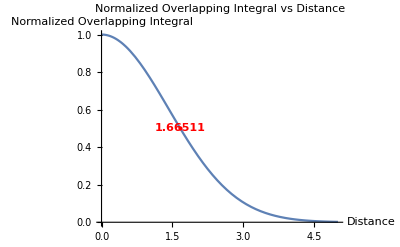

-Graphics3D-

```mathematica
(*Function to calculate and normalize the overlapping integral*)OverlappingIntegral[distance_,sigma_]:=Module[{x0,y0,x1,y1,overlappingIntegral,normalizationFactor},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Calculate the overlapping integral*)overlappingIntegral=NIntegrate[gaussian2D1[x,y]*gaussian2D2[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Calculate the normalization factor*)normalizationFactor=NIntegrate[gaussian2D1[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Normalize and return the overlapping integral*)overlappingIntegral/normalizationFactor]

(*Function to generate the 2D plot of the overlapping integral vs.distance*)
PlotOverlappingIntegral[sigma_]:=Module[{root},(*Find the distance at which the overlapping integral is 0.5*)root=FindRoot[OverlappingIntegral[d,sigma]==0.5,{d,0,5}];
(*Generate the plot and mark the point where the overlapping integral is 0.5*)Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance",Epilog->{Red,PointSize[Large],Point[{d/. root,0.5}],Text[Style[ToString[d/. root],Red,Bold],{d/. root,0.5},{-1.5,0}]}]]

(*Function to generate the 3D plot of the overlapping Gaussians*)
Plot3DOverlap[distance_,sigma_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Generate and return the 3D plot*)Plot3D[gaussian2D1[x,y]+gaussian2D2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"3D Overlap of Two Gaussian Distributions"]]

(*Call the functions to generate the plots*)
PlotOverlappingIntegral[1]
Plot3DOverlap[2,1]
```

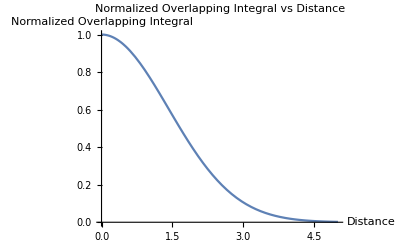

-Graphics3D-

```mathematica
(*Function to calculate and normalize the overlapping integral*)OverlappingIntegral[distance_,sigma_]:=Module[{x0,y0,x1,y1,overlappingIntegral,normalizationFactor},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Calculate the overlapping integral*)overlappingIntegral=NIntegrate[gaussian2D1[x,y]*gaussian2D2[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Calculate the normalization factor*)normalizationFactor=NIntegrate[gaussian2D1[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Normalize and return the overlapping integral*)overlappingIntegral/normalizationFactor]

(*The rest of the code remains the same as previously provided*)

(*Function to generate the 2D plot of the overlapping integral vs.distance*)
PlotOverlappingIntegral[sigma_]:=Plot[OverlappingIntegral[d,sigma],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance"]

(*Function to generate the 3D plot of the overlapping Gaussians*)
Plot3DOverlap[distance_,sigma_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Generate and return the 3D plot*)Plot3D[gaussian2D1[x,y]+gaussian2D2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"3D Overlap of Two Gaussian Distributions"]]

(*Call the functions to generate the plots*)
PlotOverlappingIntegral[1]
Plot3DOverlap[2,1]
```

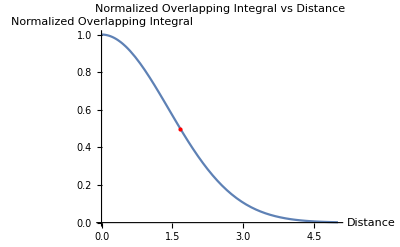

-Graphics3D-

```mathematica
(*Pre-define sigma to be 1*)sigma=1;

(*Function to calculate and normalize the overlapping integral*)
OverlappingIntegral[distance_]:=Module[{x0,y0,x1,y1,overlappingIntegral,normalizationFactor},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Calculate the overlapping integral*)overlappingIntegral=NIntegrate[gaussian2D1[x,y]*gaussian2D2[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Calculate the normalization factor*)normalizationFactor=NIntegrate[gaussian2D1[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
(*Normalize and return the overlapping integral*)overlappingIntegral/normalizationFactor]

(*The rest of the code remains the same as previously provided*)

(*Function to generate the 2D plot of the overlapping integral vs.distance*)
PlotOverlappingIntegral[]:=Plot[OverlappingIntegral[d],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance"]

(*Function to generate the 3D plot of the overlapping Gaussians*)
Plot3DOverlap[distance_]:=Module[{x0,y0,x1,y1},(*Assume one Gaussian is centered at (0,0) and the other is centered at (distance,0)*){x0,y0}={0,0};
{x1,y1}={distance,0};
(*Define the Gaussian functions*)gaussian2D1[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x0)^2+(y-y0)^2)/(2*sigma^2)];
gaussian2D2[x_,y_]:=(1/(2*Pi*sigma^2))*Exp[-((x-x1)^2+(y-y1)^2)/(2*sigma^2)];
(*Generate and return the 3D plot*)Plot3D[gaussian2D1[x,y]+gaussian2D2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotRange->All,Mesh->None,ColorFunction->"Rainbow",PlotLabel->"3D Overlap of Two Gaussian Distributions"]]

(*Function to generate the 2D plot of the overlapping integral vs.distance*)PlotOverlappingIntegral[]:=Plot[OverlappingIntegral[d],{d,0,5},AxesLabel->{"Distance","Normalized Overlapping Integral"},PlotLabel->"Normalized Overlapping Integral vs Distance",Mesh->{{0.5}},(*Specify the y-value where mesh lines will be drawn*)MeshFunctions->{#2&},(*Use the y-value of the plot to determine where to draw mesh lines*)MeshStyle->{Red,PointSize[Large]},(*Style the mesh points as large red points*)PlotRange->All]

(*The rest of your code remains unchanged*)

(*Call the functions to generate the plots*)
PlotOverlappingIntegral[]
Plot3DOverlap[2]
```